# Adversarial learning for climate research -- a metaphor using the Lorenz 96’ system

#### Baoxiang Pan 2021.11.16

## Motivations

#### To disentangle 1) internal climate variability noise, 2) external forcing, and 3) model formulation deficiency is a core topic (if not all what we do) in climate science. Currently, adversarial learning (Goodfellow et al. 2014) is arguably the most effective paradigm for learning disentanglement. Goal: Exemplify the usage of adversarial learning for disentangling different sources of uncertainties in climate studies, using a toy model of Lorenz 96’ system.

## Hopeful takeaways

#### 1. Statistical models work by extracting useful information and suppressing irrelevant information. 2. Curse of dimensionality in supervised learning ↔ bless of dimensionality in adversarial learning. 3. Mindset within and beyond supervised learning.

## What is Lorenz 96’ and Why Lorenz 96’

```mathematica
TableForm[{Map[Labeled[#[[3]],Style[Labeled[#[[1]],Style["("<>#[[4]]<>")",Bold],Bottom],FontFamily->"Arial",15],Top]&,
{{"Pierre-Simon Laplace","(1979-1827)",ImageResize[-Graphics-,300],"Laplace's demon"},
{"Henri Poincare","(1854-1912)",ImageResize[ -Graphics-,300],"3-body problem & isomorphism"},
{"Edward Lorenz","(1917-2008)",ImageResize[-Graphics-,300], "Chaos: butterfly effect"},
{"Erica Thompson","(1917-2008)",ImageResize[RemoveBackground[-Graphics-],300] ,"Hawkmoth effect"},
{"Donald Ornstein","(1917-2008)",ImageResize[-Graphics-,300] ,"Randomness & chaos"}}]},TableSpacing->{3, 5}]
```

-Graphics-Pierre-Simon Laplace(Laplace's demon) | -Graphics-Henri Poincare(3-body problem & isomorphism) | -Graphics-Edward Lorenz(Chaos: butterfly effect) | -Graphics-Erica Thompson(Hawkmoth effect) | -Graphics-Donald Ornstein(Randomness & chaos)

#### Isomorphism: a structure-preserving mapping between two structures of the same type that can be reversed by an inverse mapping.

```mathematica
-Graphics--Graphics--Graphics-
```

#### Lorenz 63’

```mathematica
form=ImageResize[-Graphics-,300];
tend = 50;
eq = {x'[t] == σ (y[t] - x[t]), y'[t] == x[t] (ρ - z[t]) - y[t], z'[t] == x[t] y[t] - β z[t]};
init = {x[0] == 10, y[0] == 10, z[0] == 10};
pars = {σ->10, ρ->28, β->8/3};
{xs, ys, zs} = NDSolveValue[{eq /. pars, init}, {x, y, z}, {t, 0, tend}];
a=Labeled[ParametricPlot3D[{xs[t], ys[t], zs[t]}, {t, 0, tend},ImageSize->300,ColorFunction->"Rainbow"],form,Left]
```

-Graphics3D--Graphics-

#### Lorenz 96’

#### State variables: X: K slowly-varying, large-scale variables (analogous to a synoptic quantity such as the static instability of the atmosphere, arranged on a latitude circle) Y: K×J fast-varying, smaller-scale variables (analogous to convective-scale quantity) Parameters: F: the large-scale forcing applied to the system h: the strength of the coupling between spatial scales b: the relative magnitudes of Y c: the evolution speed of Y

```mathematica
K=36;
J=10;
length=10;
step=0.001;
F=10;
c=10;
h=1;
b=10;

toStringX[kk_]:=ToString[If[kk≤0,K+kk,If[kk>K,kk-K,kk]]];
toStringY[kk_,jj_]:=If[jj==0,If[kk>1,ToString[kk-1]<>"a"<>ToString[J],ToString[K]<>"a"<>ToString[J]],
					If[jj>J,If[kk<K,ToString[kk+1]<>"a"<>ToString[jj-J],ToString[kk-K+1]<>"a"<>ToString[jj-J]],
					ToString[kk]<>"a"<>ToString[jj]]];
xequation=ToExpression[Table["x"<>ToString[kk]<>"'[t]==(x"<>toStringX[kk+1]<>"[t]-x"<>toStringX[kk-2]<>"[t])*x"<>toStringX[kk-1]<>"[t]-x"<>toStringX[kk]<>
      "[t]+F-h*c*("<>StringRiffle[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{jj,J}],"[t]+"]<>"[t])/J",{kk,K}]];
yequation=ToExpression[Flatten[Table["y"<>toStringY[kk,jj]<>"'[t]==-b*c*y"<>toStringY[kk,jj+1]<>"[t](y"<>toStringY[kk,jj+2]<>"[t]-y"<>toStringY[kk,jj-1]<>
      "[t])-c*y"<>toStringY[kk,jj]<>"[t]+h*c/J*x"<>ToString[kk]<>"[t]",{kk,K},{jj,J}]]];
xinitial=ToExpression[Table["x"<>ToString[kk]<>"[0]==RandomReal[{F-.1,F+.1}]",{kk,K}]];
yinitial=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj]<>"[0]==RandomReal[{-.1,.1}]",{kk,K},{jj,J}]]];
xvar=ToExpression[Table["x"<>ToString[kk],{kk,K}]];
yvar=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{kk,K},{jj,J}]]];
result=NDSolve[Join[xequation,yequation,xinitial,yinitial],Join[xvar,yvar],{t,0,length}];
base=Table[Evaluate[Map[#[t]&,xvar]/.result],{t,0,length,step}][[;;,1]];
pertubation=Table[Evaluate[Map[#[t]&,yvar]/.result],{t,0,length,step}][[;;,1]];
plot0=RemoveBackground[-Graphics-];
form=ImageResize[RemoveBackground[-Graphics-],800];
plot1=Labeled[Show[Table[RadialAxisPlot[base[[i]],PlotRange->{-F*1.5,F*1.5},GridLines->Range[-F*1.5,F*1.5,5],Axes->Automatic,
	Filling->False,
	PlotLabel->"X",
	(*PlotStyle->Blend[{Darker[Blue],Blue,White,Red,Darker[Red]},(i-1000)/1000],*)
	PlotStyle->ColorData["Rainbow"][(i-1000)/1000.],
	BaseStyle->{FontFamily->"Arial",12}],{i,1000,2000,50}],ImageSize->280],
	Labeled[Labeled[ImageCrop[Rasterize[BarLegend["Rainbow",Ticks->None,LegendLayout->"Row"]]],Style["t=0",{FontFamily->"Arial",20}],Left,Spacings->{1, 0}],
Style["t=1000",{FontFamily->"Arial",20}],Right,Spacings->{1, 0}],Bottom];
plot2=Labeled[Show[Table[RadialAxisPlot[pertubation[[i]]*F,PlotRange->{-F*1.5,F*1.5},GridLines->Range[-F*1.5,F*1.5,5],
Axes->Table[If[i==0,True,If[Mod[i,J]==0,1,False]],{i,K*J}],
	Filling->False,
	PlotLabel->"Y",
	(*PlotStyle->Blend[{Darker[Blue],Blue,White,Red,Darker[Red]},(i-1000)/1000],*)
	PlotStyle->ColorData["Rainbow"][(i-1000)/1000.],
	BaseStyle->{FontFamily->"Arial",12}],{i,1000,2000,50}],ImageSize->280],
	Labeled[Labeled[ImageCrop[Rasterize[BarLegend["Rainbow",Ticks->None,LegendLayout->"Row"]]],Style["t=0",{FontFamily->"Arial",20}],Left,Spacings->{1, 0}],
Style["t=1000",{FontFamily->"Arial",20}],Right,Spacings->{1, 0}],Bottom];
TableForm[{{form,plot0,plot1,plot2}},TableSpacing->{0, 0}]
```

-Graphics- | -Graphics- | -Graphics--Graphics-t=0t=1000 | -Graphics--Graphics-t=0t=1000

#### Applications of Lorenz 96’ for climate modeling + machine learning

```mathematica
Style[TableForm[Transpose[{{-Graphics-,"Parameter calibration using ML as\nsurrogate to accelerate calibration"},
{-Graphics-,"Parameterization replacement using ML\nto represent unresolved processes"},
{-Graphics-,"Model replacement"},
{-Graphics-,""}}],TableAlignments->Center,TableSpacing->{1, 1}],{FontFamily->"Arial",18}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
Parameter calibration using ML as
surrogate to accelerate calibration | Parameterization replacement using ML
to represent unresolved processes | Model replacement |

#### Now, let’s jump out of the box.

## Discrimination -- what you see (feature representation) depends on what you care about (loss function)

## Case 1: Initialization disturbance: the ridiculous thing we call “spinning-up” in climate simulation, and the annoying thing we call “shock” in weather-seasonal-decadal forecast

### Experimental design

#### Consider a basic Lorenz 96’ model, with X and Y coupling, and a constant F forcing, create m simulations, each simulation for n time steps. Objective: 1. Estimate how far a simulated state is away from the initialization. 2. Clarify the dependency between estimation accuracy and model complexity

### Data

#### Creating m = 10,000 simulations, each simulation for n =2,048 time steps. Initial: independently sampling each X/Y dimension (assuming a Gaussian distribution)

-Graphics-

#### Data distribution

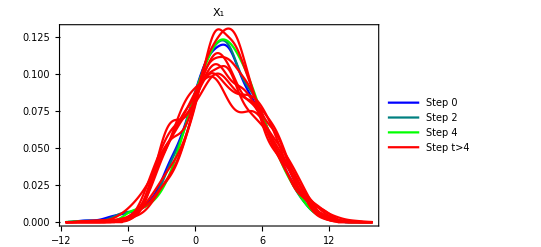
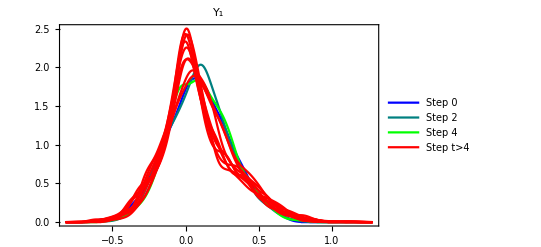
-Graphics- | -Graphics-

### Model implementation

```mathematica
net=NetChain[Flatten[{Table[{RandomSample[Range[80,150]][[1]],BatchNormalizationLayer[],Ramp,DropoutLayer[RandomReal[{.1,.3}]]},4],
			12,BatchNormalizationLayer[],SoftmaxLayer[]}],
		"Input"->36,"Output"->NetDecoder[{"Class",Range[12]}]];
Information[net,"SummaryGraphic"]
```

-Graphics-

### Results and discussion

#### Estimation based on X (K=36-dimensional)

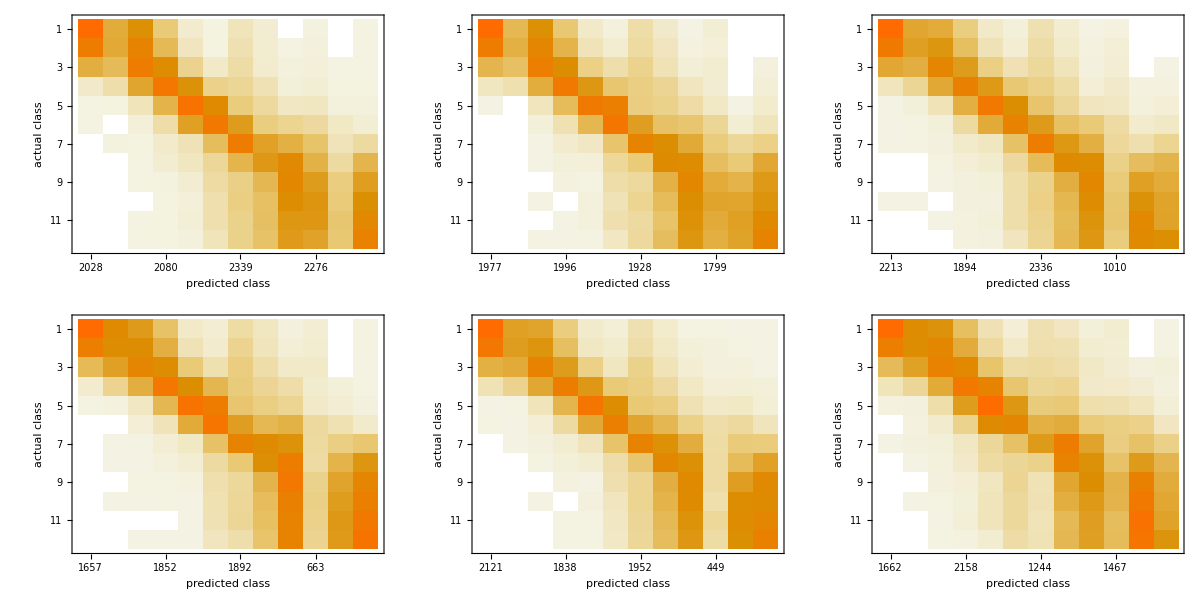

#### Estimation based on Y (K×J=36×10-dimensional)

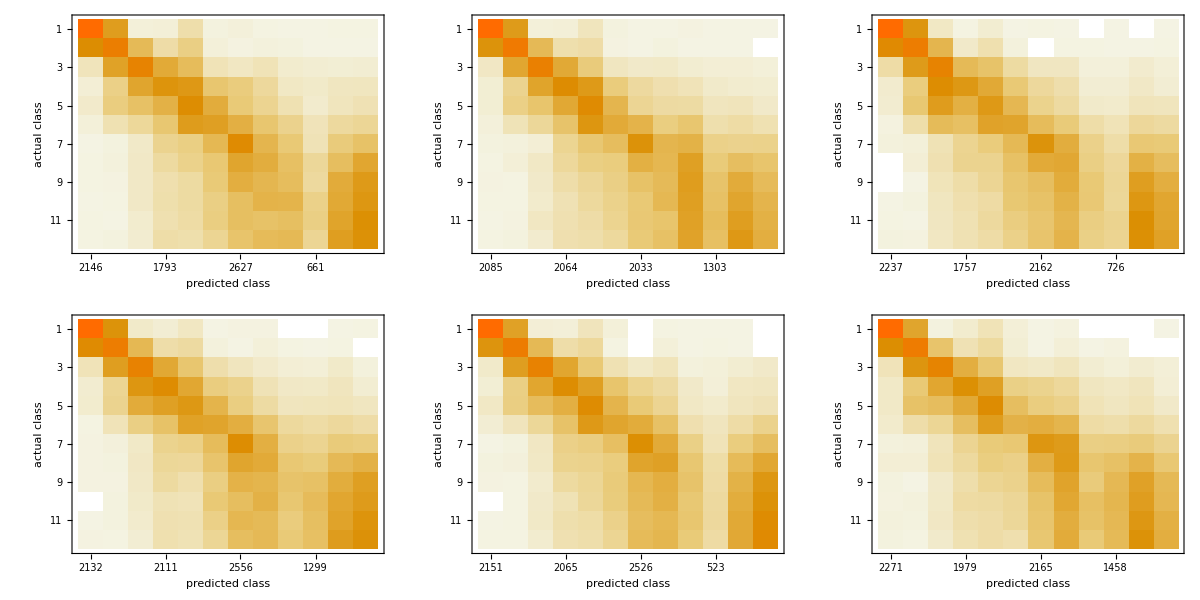

#### Impact of dimensionality

## Case 2: Hawkmoth effect: identifying model formulation deficiency in the mist of internal climate variability noise

### Experimental design

#### Consider the following three variants of Lorenz 96’ model: 1. Base model: original Lorenz 96’ model, with X and Y coupling, and a constant F forcing. 2. Reduced order model: just X, no coupling with the fast component Y. 3. Parameter-biased model: modify the parameter of the base model. 4. Structure-biased model: modify the structure form of Y for the base model. Objective: 1. Classify any chunk (t step, t from 0 to n) of simulation into the four classes above. 2. Clarify the dependency between classification accuracy and i. model complexity,s ii. model formulation difference, iii. “chunk size”.

### Results and discussion

## Case 3: Detection & Attribution of climate change: extracting external forcing information in the mist of internal climate variability noise

### Experimental design

#### Consider the following three variants of Lorenz 96’ model: 1. Base model: original Lorenz 96’ model, with X and Y coupling, and constant F forcing. 2. Reduced order model: just X, no coupling with the fast component Y. 3. Parameter-biased model: modify the parameter of the base model. 4. Structure-biased model: modify the structure form of Y for the base model. Objective: classify a chunk (t step, t from 0 to n) of simulation into the four classes above.

## Adversary

## Case 1: Overcoming the Hawkmoth effect: identifying and correcting model formulation deficiency in the mist of internal climate variability noise

## Fake it to make it

## Mission to Fulfill

## Explicitly modeling internal climate variability noise using variational inference

## Backup Code

```mathematica
K=36;
J=10;
length=1000;
step=0.01;
F=10;
c=10;
h=1;
b=10;

toStringX[kk_]:=ToString[If[kk≤0,K+kk,If[kk>K,kk-K,kk]]];
toStringY[kk_,jj_]:=If[jj==0,If[kk>1,ToString[kk-1]<>"a"<>ToString[J],ToString[K]<>"a"<>ToString[J]],
					If[jj>J,If[kk<K,ToString[kk+1]<>"a"<>ToString[jj-J],ToString[kk-K+1]<>"a"<>ToString[jj-J]],
					ToString[kk]<>"a"<>ToString[jj]]];
```

```mathematica
(*base model*)					
xequation=ToExpression[Table["x"<>ToString[kk]<>"'[t]==(x"<>toStringX[kk+1]<>"[t]-x"<>toStringX[kk-2]<>"[t])*x"<>toStringX[kk-1]<>"[t]-x"<>toStringX[kk]<>
      "[t]+F-h*c*("<>StringRiffle[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{jj,J}],"[t]+"]<>"[t])/J",{kk,K}]];
yequation=ToExpression[Flatten[Table["y"<>toStringY[kk,jj]<>"'[t]==-b*c*y"<>toStringY[kk,jj+1]<>"[t](y"<>toStringY[kk,jj+2]<>"[t]-y"<>toStringY[kk,jj-1]<>
      "[t])-c*y"<>toStringY[kk,jj]<>"[t]+h*c/J*x"<>ToString[kk]<>"[t]",{kk,K},{jj,J}]]];
xinitial=ToExpression[Table["x"<>ToString[kk]<>"[0]==RandomReal[{F-.1,F+.1}]",{kk,K}]];
yinitial=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj]<>"[0]==RandomReal[{-.1,.1}]",{kk,K},{jj,J}]]];
xvar=ToExpression[Table["x"<>ToString[kk],{kk,K}]];
yvar=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{kk,K},{jj,J}]]];

result=NDSolve[Join[xequation,yequation,xinitial,yinitial],Join[xvar,yvar],{t,0,length}];
base=Table[Evaluate[Map[#[t]&,xvar]/.result],{t,0,length,step}][[;;,1]];
pertubation=Table[Evaluate[Map[#[t]&,yvar]/.result],{t,0,length,step}][[;;,1]];
```

```mathematica
meanvarBase={Mean[base],Sqrt[Variance[base]]};
meanvarPertubation={Mean[pertubation],Sqrt[Variance[pertubation]]};
```

```mathematica
(*Export["/Users/lambda/Documents/NAS/Data/Initialization/meanvar.mx",
 <|"meanvarBase"->meanvarBase,
  "meanvarPertubation"->meanvarPertubation|>];*)
```

```mathematica
step=0.01;
length=step*2^12;
```

```mathematica
xvar=ToExpression[Table["x"<>ToString[kk],{kk,K}]];
yvar=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj],{kk,K},{jj,J}]]];
```

```mathematica
xinitial=ToExpression[Table["x"<>ToString[kk]<>"[0]==RandomVariate[NormalDistribution[meanvarBase[[1,"<>ToString[kk]<>"]],meanvarBase[[2,"<>ToString[kk]<>"]]]]",{kk,K}]];
yinitial=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj]<>"[0]==RandomVariate[NormalDistribution[meanvarPertubation[[1,"<>ToString[(kk-1)*J+jj]<>"]],meanvarPertubation[[2,"<>ToString[(kk-1)*J+jj]<>"]]]]",{kk,K},{jj,J}]]];
result=NDSolve[Join[xequation,yequation,xinitial,yinitial],Join[xvar,yvar],{t,0,length}];
```

```mathematica
seq=Prepend[Table[RandomSample[Range[2^i,2^(i+1)-1]][[1]],{i,11}],1];
base=Table[Evaluate[Map[#[t]&,xvar]/.result],{t,seq*step}][[;;,1]];
pertubation=Table[Evaluate[Map[#[t]&,yvar]/.result],{t,seq*step}][[;;,1]];
```

```mathematica
idata=Table[Block[{tempt,id=StringSplit[CreateUUID[],"-"][[1]]},
 Print[ti];
 tempt=Table[Block[{xinitial,yinitial,result,seq,base,pertubation},
	xinitial=ToExpression[Table["x"<>ToString[kk]<>"[0]==RandomVariate[NormalDistribution[meanvarBase[[1,"<>ToString[kk]<>"]],meanvarBase[[2,"<>ToString[kk]<>"]]]]",{kk,K}]];
	yinitial=ToExpression[Flatten[Table["y"<>ToString[kk]<>"a"<>ToString[jj]<>"[0]==RandomVariate[NormalDistribution[meanvarPertubation[[1,"<>ToString[(kk-1)*J+jj]<>"]],meanvarPertubation[[2,"<>ToString[(kk-1)*J+jj]<>"]]]]",{kk,K},{jj,J}]]];
	result=NDSolve[Join[xequation,yequation,xinitial,yinitial],Join[xvar,yvar],{t,0,length}];
	seq=Prepend[Table[RandomSample[Range[2^i,2^(i+1)-1]][[1]],{i,11}],1];
	base=Table[Evaluate[Map[#[t]&,xvar]/.result],{t,seq*step}][[;;,1]];
	pertubation=Table[Evaluate[Map[#[t]&,yvar]/.result],{t,seq*step}][[;;,1]];
	{all,seq,base,pertubation}],{all,100}];
 Export["/Users/lambda/Documents/NAS/Data/Initialization/"<>id<>".mx",tempt]],{ti,100}];
```

```mathematica
SetDirectory["/Users/lambda/Documents/NAS/Data/Initialization"];
(*files=Select[FileNames["*mx"],Not[#=="meanvar.mx"]&][[1;;100]];
Export["/Users/lambda/Documents/NAS/Data/Initialization/seq.mx",files];*)
files=Import["/Users/lambda/Documents/NAS/Data/Initialization/seq.mx"];
{basedata,pertubationdata}=Block[{tempt,basedata,pertubationdata},
	tempt=Flatten[Table[Import[files[[i]]],{i,Length[files]}],1];
	basedata=Table[Table[tempt[[i,3]][[j]]->j,{j,12}],{i,Length[tempt]}];
	pertubationdata=Table[Table[tempt[[i,4]][[j]]->j,{j,12}],{i,Length[tempt]}];
	{basedata,pertubationdata}];
```

```mathematica
tempt=Flatten[Table[Import[files[[i]]],{i,Length[files]}],1];
```

```mathematica
training=RandomSample[Flatten[basedata[[1;;6000]],1]];
validation=RandomSample[Flatten[basedata[[6001;;8000]],1]];
test=RandomSample[Flatten[basedata[[8001;;]],1]];
Table[Block[{id,net,trained},
	id=StringSplit[CreateUUID[],"-"][[1]];
	net=NetChain[Flatten[{Table[{RandomSample[Range[80,150]][[1]],BatchNormalizationLayer[],Ramp,DropoutLayer[RandomReal[{.1,.3}]]},4],12,BatchNormalizationLayer[],SoftmaxLayer[]}],
		"Input"->Length[training[[1,1]]],"Output"->NetDecoder[{"Class",Range[12]}]];
	net=NetInitialize[net];
	trained=NetTrain[net,training,ValidationSet->validation,MaxTrainingRounds->1000,BatchSize->256];
Export["/Users/lambda/Documents/NAS/Data/Initialization/Trained_"<>id<>".mx",trained];],{iii,10}];
trained=Map[Import,FileNames["Trained*mx"]];
```

```mathematica
trained=Map[Import,FileNames["Trained*mx"]];
TableForm[ArrayReshape[Table[cm = ClassifierMeasurements[trained[[i]], test];cm["ConfusionMatrixPlot"],{i,6}],{2,3}]]
```

```mathematica
training=RandomSample[Flatten[pertubationdata[[1;;6000]],1]];
validation=RandomSample[Flatten[pertubationdata[[6001;;8000]],1]];
test=RandomSample[Flatten[pertubationdata[[8001;;]],1]];
Table[Block[{id,net,trained},
	id=StringSplit[CreateUUID[],"-"][[1]];
	net=NetChain[Flatten[{Table[{RandomSample[Range[80,350]][[1]],BatchNormalizationLayer[],Ramp,DropoutLayer[RandomReal[{.1,.3}]]},4],12,BatchNormalizationLayer[],SoftmaxLayer[]}],
		"Input"->Length[training[[1,1]]],"Output"->NetDecoder[{"Class",Range[12]}]];
	net=NetInitialize[net];
	trained=NetTrain[net,training,ValidationSet->validation,MaxTrainingRounds->1000,BatchSize->256];
Export["/Users/lambda/Documents/NAS/Data/Initialization/Y_Trained_"<>id<>".mx",trained];],{iii,10}];
```

```mathematica
trained=Map[Import,FileNames["Y_Trained*mx"]];
TableForm[ArrayReshape[Table[cm = ClassifierMeasurements[trained[[i]], test];cm["ConfusionMatrixPlot"],{i,6}],{2,3}]]
```

-Graphics-

#### Visualizations

```mathematica
TableForm[ArrayReshape[Table[ListLinePlot[base[[;;,i]],AspectRatio->1/4,Frame->True,
FrameLabel->{{"\!\(\*SubscriptBox[\(x\), \("<>ToString[i]<>"\)]\)",None},{"Time Step",None}},PlotRange->{All,{-15,15}},
ImageSize->300,BaseStyle->{FontName->"Arial",12}],{i,1,36,2}],{4,4}],TableSpacing->{-1, -1}]
```

```mathematica
TableForm[ArrayReshape[Table[ListLinePlot[pertubation[[;;,i]],AspectRatio->1/4,Frame->True,
FrameLabel->{{"\!\(\*SubscriptBox[\(y\), \("<>ToString[i]<>"\)]\)",None},{"Time Step",None}},PlotRange->{All,{-1,1}},
ImageSize->300,BaseStyle->{FontName->"Arial",12}],{i,1,360,18}],{4,4}],TableSpacing->{-1, -1}]
```

```mathematica
TableForm[ArrayReshape[Table[Show[{RadialAxisPlot[base[[i]],PlotLabel->"Time Step: "<>ToString[i],Axes->Automatic,PlotRange->{-12,12},GridLines->Range[-12,12,4],Filling->None],
RadialAxisPlot[pertubation[[i]]*F,PlotLabel->"Time Step: "<>ToString[i],Axes->False,GridLines->None,Filling->None,PlotStyle->{Red,Opacity[0.5]}]}],
{i,Table[2^i,{i,0,11}]}],{2,6}],TableSpacing->{0, 0}]
```

```mathematica
var=1;
TableForm[{{SmoothHistogram[Table[basedata[[1;;-1;;10,class,1,var]],{class,12}],PlotStyle->Join[{Blue,Blend[{Blue,Green},.5],Green},Table[Red,9]],
Frame->True,
PlotLabel->"X_1",
BaseStyle->{FontFamily->"Arial",15},
ImageSize->400,
PlotLegends->{"Step 0","Step 2","Step 4","Step t>4"}],
SmoothHistogram[Table[pertubationdata[[1;;-1;;10,class,1,var]],{class,12}],PlotStyle->Join[{Blue,Blend[{Blue,Green},.5],Green},Table[Red,9]],
Frame->True,
PlotLabel->"Y_1",
BaseStyle->{FontFamily->"Arial",15},
ImageSize->400,
PlotLegends->{"Step 0","Step 2","Step 4","Step t>4"}]}}]
```